```mathematica
BlockSVDPowerMethod[A_,s_,precision_]:=(
err=∞;


VV=Table[If[i==j||i>Dimensions[A][[
1]]||j>Dimensions[A][[1]],1,0],{i,s},{j,Dimensions[A][[1]]}];


While[err>precision,
{Q,R}=QRDecomposition[A.VV];
Q=Transpose[Q];
U=Q[[All,1;;s]];

{Q,R}=QRDecomposition[Transpose[A].U];
Q=Transpose[Q];
VV=Q[[All,1;;s]];
Σ1=R[[1;;s,1;;s]];
err=Norm[A.VV-U.Σ1];
];
{U,Σ1,VV}
)
GenerateInitialGuess[s_,width_]:=(
Table[If[i==j||i>width||j>width,1,0],{i,width},{j,s}]
)


Cat=ImageData[-Graphics-];
Dimensions[Cat]
{U,Σ,V}=SingularValueDecomposition[Cat[[All,All,1]]];
```

{2,3,4}

```mathematica
Vt=Transpose[V];
Dimensions[Vt]
```

{3,3}

```mathematica
Dimensions[Vt[[All,1;;20]]]
```

Part::take: Cannot take positions 1 through 20 in «1».

{3}

```mathematica
err
```

err

```mathematica
Dimensions[V]
```

{3,3}

```mathematica
Dimensions[QRDecomposition[CatRed.VV]]
```

{1}

```mathematica
GenerateInitialGuess[width,SVDThreshold]//MatrixForm;
```

Table::iterb: Iterator {i,SVDThreshold} does not have appropriate bounds.

```mathematica
CatRed=Cat[[All,All,1]];
Dimensions[CatRed]
```

{2,3}

```mathematica
{20,37}
Dimensions[initialGuess]
```

{20,37}

```mathematica
({{1, 2}, {3, 4}, {5, 6}})({{1, 2}, {3, 4}, {5, 6}});
A=({{1, 2}, {3, 4}, {5, 6}});
Dimensions[({{1, 2}, {3, 4}, {5, 6}})]
```

```mathematica
s=1;
```

```mathematica
VVrowsNum=Dimensions[A][[2]];
VV=Table[If[i==j||i>VVrowsNum||j>VVrowsNum,1,0],{i,VVrowsNum},{j,s}]
```

{{1},{0}}

```mathematica
dim = Dimensions[CatRed]
```

{2,3}

```mathematica
width=Dimensions[CatRed][[2]];
height=Dimensions[CatRed][[1]];
SVDThreshold=2;
```

```mathematica
CatGreen=Cat[[All,All,2]];
```

```mathematica
CatBlue=Cat[[All,All,3]];
(*initialGuess=Vt[[All,1;;20]];*)
```

```mathematica
initialGuess=GenerateInitialGuess[SVDThreshold,width];

precision=0.3;
SVDCatRed=BlockSVDPowerMethod[CatRed,SVDThreshold,precision];
SVDCatBlue=BlockSVDPowerMethod[CatBlue,SVDThreshold,precision];
SVDCatGreen=BlockSVDPowerMethod[CatGreen,SVDThreshold,precision];


(*SVDCatRed=SingularValueDecomposition[CatRed,SVDThreshold];*)
```

Dot::dotsh: Tensors {{0.188235,0.188235,0.188235},{0.188235,«20»,0.188235}} and {{1,0},{0,1}} have incompatible shapes.

Set::shape: Lists {Q,R} and QRDecomposition[{{0.188235,0.188235,0.188235},«1»}.{{1,0},{0,1}}] are not the same shape.

$RecursionLimit::reclim2: Recursion depth of 1024 exceeded during evaluation of Transpose[Q].

Dot::dotsh: Tensors {{0.254902,0.254902,0.254902},{0.254902,«19»,0.254902}} and {{1,0},{0,1}} have incompatible shapes.

Set::shape: Lists {Q,R} and QRDecomposition[{{0.254902,0.254902,0.254902},{0.254902,«19»,«19»}}.{«1»}] are not the same shape.

Dot::dotsh: Tensors {{0.380392,0.380392,0.380392},{0.380392,«19»,0.380392}} and {{1,0},{0,1}} have incompatible shapes.

Set::shape: Lists {Q,R} and QRDecomposition[{{0.380392,0.380392,0.380392},{0.380392,«19»,«19»}}.{«1»}] are not the same shape.

```mathematica
(*SVDCatBlue=SingularValueDecomposition[CatBlue,SVDThreshold];*)
```

```mathematica
(*SVDCatGreen=SingularValueDecomposition[CatGreen,SVDThreshold];*)
Σ =SVDCatRed[[2]];
```

```mathematica
U=SVDCatRed[[1]];
```

```mathematica
VTr=Transpose[SVDCatRed[[3]]];
Dimensions[Σ]
```

{2,2}

```mathematica
Dimensions[U]
```

{2,2}

```mathematica
Dimensions[VTr]
```

{2,3}

```mathematica
x=60;
(s^2+x*s+s*x)*3
```

3 (120 s+s^2)

```mathematica
1107*4
```

4428

```mathematica
SVDCatRedMult=U.Σ .VTr;
```

```mathematica
Image[SVDCatRedMult]
```

-Graphics-

```mathematica
SingValuesRed=Diagonal[Σ];
```

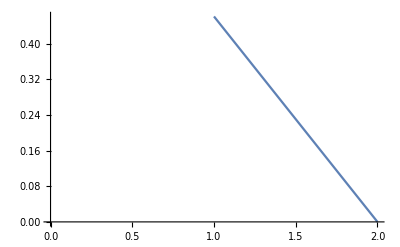

```mathematica
ListLinePlot[SingValuesRed]
```

```mathematica
ΣBlue =SVDCatBlue[[2]];
```

```mathematica
UBlue=SVDCatBlue[[1]];
```

```mathematica
VTrBlue=Transpose[SVDCatBlue[[3]]];

SVDCatBlueMult=UBlue.ΣBlue .VTrBlue;
```

```mathematica
Image[SVDCatBlueMult]
```

-Graphics-

```mathematica
SingValuesBlue=Diagonal[ΣBlue];
```

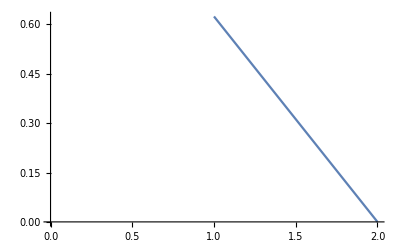

```mathematica
ListLinePlot[SingValuesBlue]
```

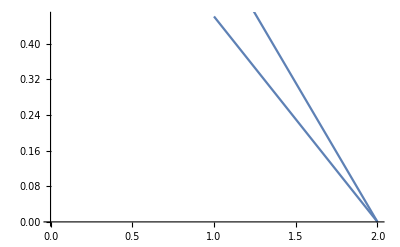

```mathematica
Show[ListLinePlot[SingValuesRed],ListLinePlot[SingValuesBlue]]
```

```mathematica
ΣGreen =SVDCatGreen[[2]];
UGreen=SVDCatGreen[[1]];
```

```mathematica
VTrGreen=Transpose[SVDCatGreen[[3]]];
```

```mathematica
SVDCatGreenMult=UGreen.ΣGreen .VTrGreen;
SingValuesGreen=Diagonal[ΣGreen];
```

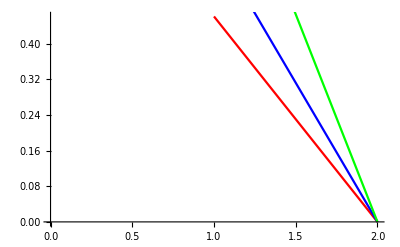

```mathematica
Show[ListLinePlot[SingValuesRed,PlotStyle->Red],ListLinePlot[SingValuesBlue,PlotStyle->Blue],ListLinePlot[SingValuesGreen,PlotStyle->Green]]
```

```mathematica
Image[SVDCatGreenMult]
```

-Graphics-

```mathematica
dim=Dimensions[Cat];
m=dim[[1]];
n=dim[[2]];
FinalSVDCat=Table[0,{i,m},{j,n}];
For[i=1,i≤m,i++,
For[j=1,j≤n,j++,
r=SVDCatRedMult[[i,j]];
g=SVDCatGreenMult[[i,j]];
b=SVDCatBlueMult[[i,j]];
FinalSVDCat[[i,j]]={r,g,b};
]
]
```

```mathematica
Image[FinalSVDCat]
```

-Graphics-

```mathematica
Export["lady4.jpg",-Graphics-]
```

lady4.jpg

```mathematica
Export["lady2.jpg",-Graphics-]
```

lady2.jpg

```mathematica
Export["lady.jpg",-Graphics-]
```

lady.jpg

```mathematica
Export["example1.png",Plot[Exp[x],{x,0,3}]]
```

example1.png